```mathematica
Needs@"MATLink`";
```

```mathematica
OpenMATLAB[]
```

```mathematica
MEvaluate["cd "<>FileNameJoin@{NotebookDirectory[],"Galpha-Gbeta"}];
intgreen=MFunction["int_green3d_tri","OutputArguments"->2];
potential=MFunction["potential"];
```

```mathematica
NormalVector=Normalize@Cross[#⟦2⟧-#⟦1⟧,#⟦3⟧-#⟦1⟧]&;
NodesElements={MeshCoordinates@#, Reverse/@MeshCells[#,2]⟦All,1⟧}&;
```

```mathematica
SetDirectory@NotebookDirectory[];
```

## Sphere

```mathematica
model=ConnectedMeshComponents@Import@"sphere.stl"
```

{-Graphics3D-}

```mathematica
voltages={1};
```

```mathematica
{nodes,elements}=(NodesElements/@model)ᵀ;
elements+=Prepend[Accumulate@Most[Length/@nodes],0];
nodes=Join@@nodes;
```

```mathematica
Export["sphere.csv",StringJoin@@Riffle[Join[{ToString@Length@nodes<>","<>ToString@Length@elements,ExportString[nodes,"CSV"]},Flatten[{ToString@Length@#,ExportString[#,"CSV"]}&/@((Reverse/@#)&/@elements),1],{ExportString[{{-2,-2,0},{2,2,0},{20,20,1}},"CSV"]}],"\n"],"Text"];
```

```mathematica
elements=Join@@Table[Join[#,{1,voltages⟦i⟧}]&/@elements⟦i⟧,{i,Length@elements}];
triangles=nodes⟦#⟧&/@elements⟦All,1;;3⟧;
```

```mathematica
Export["nodes.csv",nodes];
Export["elements.csv",elements];
```

### BEM

```mathematica
Run["BEM sphere.csv"];
```

```mathematica
path=FileNameJoin@{NotebookDirectory[],"sphere"};
```

```mathematica
data=Import[path,"Byte"];
pos=Prepend[Flatten@Position[data,10,1,7],0];
{n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum}=Read[StringToStream@FromCharacterCode@data⟦#⟧,Number]&/@(Span@@(#+{1,-1})&/@Partition[pos,2,1]);
data=Partition[ImportString[FromCharacterCode@data⟦Last@pos+1;;-1⟧,"Real64"],n];
```

```mathematica
4π data⟦1⟧
```

{0.990299,0.989074,0.982443,1.02224,0.978183,0.977449,0.978063,0.977388,0.977864,0.977457,0.973229,0.973186,0.973318,0.973241,0.973356,0.973254,1.0195,0.993774,1.00148,0.985969,1.00049,0.985906,1.00035,0.98522,1.00192,1.02222,1.01936,1.00464,1.00385,1.00378,1.00228,1.00476,1.00311,1.00104,1.01129,1.01114,1.00089,1.01169,1.00957,1.01455,1.01343,1.01329,1.01022,1.01024,1.01349,1.01606,1.01515,1.01548,1.01458,1.01449,1.01542,1.02591,1.02508,1.02547,1.0087,1.01551,1.0153,1.00922,1.01392,0.998223,1.00958,1.00964,1.00953,1.0097,1.00959,1.00983,1.01543,1.01528,1.01529,1.01561,1.01542,1.01567,1.02454,1.02489,1.02355,1.0248,1.02358,1.02358,1.02431,1.02222,1.01662,0.99029,0.989086,0.982434,1.02221,0.977417,0.978034,0.977405,0.977413,0.977916,0.978169,0.97332,0.973325,0.973244,0.97326,0.973263,0.973301,1.01953,0.993803,1.00146,0.985932,1.00049,0.985903,1.00036,0.985233,1.00193,1.02217,1.01937,1.00373,1.00231,1.0047,1.00464,1.00318,1.00389,1.01171,1.01112,1.00959,1.00109,1.01131,1.00091,1.01332,1.0102,1.01455,1.01349,1.01028,1.01351,1.01604,1.01543,1.01454,1.01512,1.01449,1.01542,1.02518,1.02539,1.02577,1.00915,1.01523,1.00873,1.0155,0.998249,1.01395,1.00949,1.00968,1.00958,1.0096,1.00969,1.00951,1.01548,1.01532,1.01524,1.01561,1.01545,1.01559,1.02462,1.02481,1.02351,1.02358,1.02476,1.02361,1.02218,1.01661,1.02437,0.98697,0.986987,0.986994,1.01977,1.01974,1.01977,0.977895,0.977443,0.977891,0.977385,0.977546,0.978036,0.973297,0.973268,0.973214,0.973248,0.973362,0.973267,1.00143,0.987515,1.00147,0.987547,0.987565,1.00149,1.01516,1.01517,1.01514,1.00314,1.0023,1.00225,1.00309,1.00326,1.00239,1.01155,1.01152,1.00941,1.01153,1.00939,1.00938,1.01374,1.01291,1.01379,1.01297,1.01294,1.01382,1.01587,1.01496,1.01596,1.01504,1.015,1.01592,1.02522,1.0252,1.0251,1.01313,0.999142,0.999188,1.01317,0.999208,1.01317,1.00961,1.00959,1.00973,1.00963,1.0096,1.00964,1.01559,1.01533,1.01538,1.01546,1.01539,1.01552,1.02456,1.02473,1.02364,1.02461,1.02354,1.02354,1.01271,1.01269,1.01276,0.990274,0.989059,0.982504,1.02218,0.978043,0.977973,0.977534,0.977459,0.978022,0.977482,0.973286,0.97332,0.973252,0.973331,0.973324,0.973322,0.993932,1.01969,1.00046,0.985874,0.999999,0.984658,0.986442,1.00185,1.02217,1.01994,1.00134,1.00233,1.00475,1.00373,1.00318,1.00374,1.00476,1.01163,1.00104,1.01125,1.00088,1.01133,1.00956,1.01323,1.01011,1.01375,1.01028,1.01451,1.01349,1.01608,1.01519,1.01546,1.01536,1.01459,1.01446,1.02522,1.02591,1.02537,1.01524,1.00914,1.01557,1.0088,1.01394,0.998216,1.00971,1.00964,1.00965,1.00965,1.00967,1.00961,1.01555,1.01537,1.01555,1.01555,1.01534,1.01533,1.02466,1.02363,1.02473,1.02471,1.02362,1.02357,1.02219,1.02411,1.01667,0.990302,0.989094,0.982458,1.02221,0.978091,0.977483,0.978109,0.977942,0.977442,0.977502,0.973376,0.973303,0.973394,0.973334,0.973277,0.973245,0.993784,1.01949,0.985204,1.00032,1.00053,0.985947,1.00152,0.986011,1.02219,1.01937,1.00191,1.00379,1.00316,1.0038,1.00466,1.00474,1.00239,1.01171,1.0113,1.00105,1.01113,1.00962,1.00089,1.01016,1.01328,1.01352,1.01348,1.01027,1.0146,1.01539,1.01448,1.01453,1.01514,1.01544,1.01608,1.02528,1.02584,1.02547,1.01526,1.00917,1.01394,0.998192,1.00875,1.01552,1.00976,1.00974,1.00953,1.00959,1.00966,1.00975,1.01537,1.01563,1.01566,1.01529,1.01553,1.01533,1.02357,1.02354,1.02479,1.02464,1.0236,1.02486,1.02221,1.01656,1.02438,0.986957,0.98699,0.987016,1.01974,1.01973,1.01978,0.977326,0.978006,0.977445,0.977866,0.978006,0.977443,0.973284,0.973205,0.973368,0.973321,0.973248,0.973318,1.00141,0.987497,0.987515,1.00143,0.987533,1.00146,1.01516,1.01516,1.01516,1.00216,1.00228,1.0032,1.00229,1.0031,1.0032,1.01144,1.00932,1.00938,1.00931,1.01147,1.01157,1.01374,1.0138,1.01297,1.01372,1.01291,1.01286,1.01593,1.01498,1.01589,1.01502,1.01585,1.01495,1.02517,1.02523,1.02507,1.01315,0.999162,0.999205,1.01317,1.01316,0.999203,1.00966,1.00966,1.00972,1.00972,1.00954,1.00961,1.01545,1.01533,1.01535,1.01555,1.01561,1.01536,1.02454,1.02471,1.02469,1.02352,1.02356,1.02349,1.0127,1.01269,1.01276,0.990281,0.989098,0.982421,1.02221,0.977984,0.977514,0.977538,0.978059,0.977432,0.977901,0.97329,0.973277,0.973171,0.973233,0.97326,0.973362,0.993776,1.01949,0.98599,1.00149,1.0005,0.985917,1.00036,0.985221,1.0019,1.02217,1.01938,1.0023,1.00371,1.00482,1.0038,1.00479,1.0032,1.00961,1.01174,1.00108,1.01116,1.01136,1.0009,1.01014,1.01328,1.01459,1.01348,1.01353,1.01027,1.0161,1.01517,1.01451,1.01539,1.01541,1.01453,1.02519,1.02592,1.02537,1.00916,1.01527,1.00875,1.01553,1.01397,0.998244,1.00972,1.00958,1.00966,1.00964,1.00961,1.00962,1.01555,1.01529,1.0156,1.01554,1.01544,1.01534,1.0236,1.02466,1.02466,1.02483,1.02356,1.02373,1.02217,1.0166,1.02435,0.989084,0.990295,0.982478,1.02217,0.977374,0.977417,0.977853,0.978113,0.97815,0.977475,0.973202,0.973268,0.97319,0.97337,0.973314,0.973277,0.993932,1.0197,1.0018,0.9864,0.984631,0.999978,0.985895,1.00047,1.00131,1.01995,1.0222,1.00225,1.00464,1.0038,1.00475,1.00311,1.00384,1.00107,1.00955,1.01127,1.01169,1.00087,1.01122,1.0137,1.01025,1.01443,1.01347,1.0133,1.01024,1.0161,1.01515,1.01542,1.01452,1.01545,1.01454,1.02588,1.02542,1.02509,1.01531,1.00921,1.01553,1.00876,0.998213,1.01392,1.00956,1.0095,1.00975,1.00974,1.00956,1.00958,1.01542,1.01525,1.01565,1.01562,1.01535,1.01536,1.02454,1.02481,1.0236,1.02355,1.02486,1.02353,1.02218,1.02414,1.01668}

```mathematica
points=Mean/@triangles;
{Min@#,Max@#}&/@(pointsᵀ)
```

{{-0.971663,0.971672},{-0.971668,0.971649},{-0.971639,0.971663}}

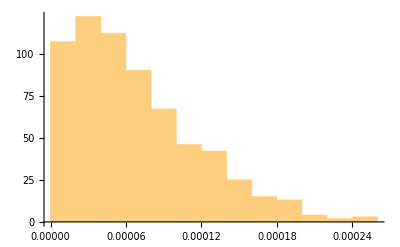

```mathematica
part=All;
Histogram[100Abs[potential[triangles,4π data⟦1⟧,points⟦part⟧]-1]/1]
```

```mathematica
points=Flatten[Table[{x,y,0},{x,-2,2,0.1},{y,-2,2,0.1}],1];
data=Flatten/@({points⟦All,1;;2⟧,Re@potential[triangles,4π data⟦1⟧,points]}ᵀ);
```

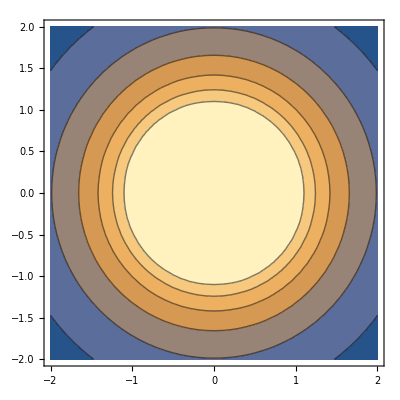

```mathematica
ListContourPlot[data,Contours->Automatic]
```

```mathematica
data=Import[path<>"calc","Byte"];
pos=Prepend[Flatten@Position[data,10,1,16],0];
{n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum,xmin,xmax,nx,ymin,ymax,ny,zmin,zmax,nz}=Read[StringToStream@FromCharacterCode@data⟦#⟧,Number]&/@(Span@@(#+{1,-1})&/@Partition[pos,2,1]);
data=Partition[#,nx*ny*nz]&/@Partition[ImportString[FromCharacterCode@data⟦Last@pos+1;;-1⟧,"Real64"],nx*ny*nz*amountOfElectrodes];
```

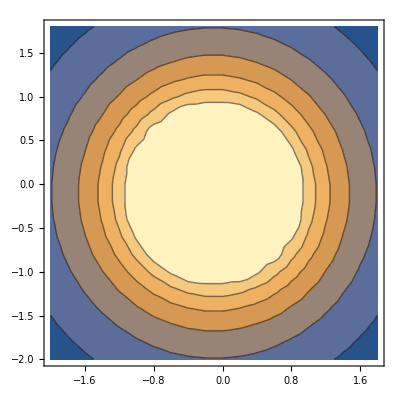

```mathematica
ListContourPlot[Flatten/@({N@Tuples[{xmin+(xmax-xmin)/nx Range[0,nx-1],ymin+(ymax-ymin)/ny Range[0,ny-1]}],data⟦1,1⟧}ᵀ)]
```

### 3D_Potential_CHBIE_FMM

```mathematica
Run["python run.py sphere"];
Run["3D_Potential_CHBIE_FMM_64"];
```

```mathematica
output=Import["output.dat","Table"];
values=Rest/@output⟦3;;-1⟧;
charges=values⟦All,2⟧;
```

```mathematica
charges
```

{0.967208,0.966381,0.961965,0.987334,0.955636,0.955264,0.955498,0.955182,0.955352,0.955247,0.942787,0.94277,0.9429,0.942844,0.942905,0.942845,0.985082,0.969498,0.973839,0.964037,0.973885,0.964757,0.973468,0.96445,0.97309,0.987084,0.986108,0.974682,0.974643,0.974567,0.973821,0.974746,0.974196,0.973942,0.980907,0.980764,0.97385,0.981526,0.981087,0.983249,0.98379,0.982617,0.982502,0.982499,0.982724,0.98507,0.984429,0.984727,0.984136,0.984125,0.984711,0.989337,0.989062,0.989339,0.981897,0.983446,0.983394,0.98215,0.983881,0.973744,0.977986,0.978034,0.977957,0.978097,0.977993,0.978216,0.980829,0.980815,0.980813,0.980984,0.980918,0.981054,0.986805,0.987139,0.98641,0.986994,0.986536,0.986439,0.990149,0.988821,0.982906,0.967212,0.966393,0.961977,0.987334,0.955257,0.955505,0.955213,0.955209,0.955422,0.955626,0.94291,0.942917,0.942812,0.942831,0.942855,0.942877,0.985096,0.969515,0.973826,0.964015,0.973895,0.964769,0.973461,0.96444,0.973107,0.987075,0.986116,0.974556,0.973829,0.974695,0.97469,0.97424,0.974691,0.981531,0.980755,0.981091,0.97398,0.98093,0.973865,0.982646,0.98249,0.983248,0.983842,0.982519,0.982736,0.985068,0.984704,0.984119,0.984414,0.984102,0.984706,0.989119,0.989353,0.989254,0.982111,0.983362,0.981911,0.983441,0.973777,0.98391,0.977929,0.978084,0.978021,0.978037,0.978119,0.977947,0.980872,0.980835,0.980772,0.981001,0.980956,0.980961,0.986869,0.987081,0.986392,0.98642,0.986978,0.986569,0.988814,0.982909,0.990173,0.965277,0.965304,0.965305,0.98607,0.986068,0.986079,0.955415,0.955225,0.955377,0.95517,0.955312,0.955518,0.942891,0.942866,0.942845,0.942825,0.942914,0.942828,0.974417,0.96518,0.97445,0.965208,0.965236,0.974473,0.98183,0.981836,0.981834,0.974214,0.973811,0.973786,0.974185,0.974305,0.973893,0.981466,0.98146,0.98094,0.98146,0.980938,0.980934,0.982857,0.983536,0.982891,0.983574,0.98357,0.982915,0.984936,0.984276,0.984992,0.984324,0.984318,0.984984,0.989142,0.989112,0.989058,0.983604,0.974456,0.974477,0.983625,0.974484,0.983625,0.978013,0.978009,0.978147,0.978026,0.978052,0.978061,0.981,0.980855,0.980904,0.98088,0.980919,0.980943,0.986854,0.987003,0.98658,0.986913,0.986499,0.986499,0.981431,0.981438,0.981456,0.96719,0.966395,0.961992,0.987304,0.955513,0.955409,0.955316,0.955221,0.955456,0.955296,0.942841,0.942857,0.942829,0.94289,0.942889,0.942866,0.969627,0.985238,0.973865,0.964743,0.973201,0.964003,0.964428,0.974156,0.987067,0.986471,0.972747,0.973836,0.974757,0.974544,0.974221,0.97452,0.974767,0.981478,0.973946,0.980911,0.973853,0.980865,0.981075,0.982589,0.982442,0.982822,0.982529,0.983268,0.983844,0.985088,0.984449,0.984735,0.984675,0.984173,0.984095,0.989087,0.989359,0.989258,0.983348,0.982097,0.983485,0.981943,0.983889,0.973766,0.978078,0.978023,0.978049,0.978062,0.978064,0.978021,0.980945,0.980883,0.98093,0.980943,0.980864,0.980862,0.9869,0.986477,0.986939,0.986995,0.986478,0.98653,0.988806,0.989993,0.982967,0.967204,0.966385,0.961992,0.987332,0.955528,0.955286,0.955562,0.955419,0.955269,0.955261,0.942938,0.942842,0.942931,0.942913,0.942853,0.942809,0.969514,0.985092,0.964421,0.973441,0.973917,0.964795,0.973883,0.964092,0.987078,0.986112,0.973108,0.974583,0.97422,0.974593,0.974727,0.974763,0.973883,0.981525,0.980914,0.97396,0.980761,0.981109,0.973863,0.98247,0.98262,0.982731,0.983832,0.982507,0.983298,0.984678,0.984096,0.984118,0.984442,0.984716,0.985094,0.989169,0.989363,0.989324,0.983371,0.982119,0.983896,0.973739,0.981913,0.983445,0.978115,0.978139,0.977968,0.977977,0.978047,0.978132,0.98087,0.980999,0.981036,0.980807,0.980919,0.980871,0.986434,0.986521,0.987014,0.986888,0.986455,0.987082,0.988822,0.982893,0.990171,0.965263,0.965284,0.965291,0.986059,0.986048,0.98606,0.95513,0.955456,0.955217,0.955338,0.955474,0.955212,0.942843,0.942804,0.942926,0.942902,0.942821,0.942863,0.974392,0.965156,0.965182,0.974416,0.965201,0.974445,0.981816,0.981823,0.981815,0.973707,0.973802,0.974249,0.973826,0.97416,0.974271,0.981396,0.980883,0.980921,0.980893,0.981426,0.981477,0.982843,0.982908,0.983565,0.98285,0.983547,0.983506,0.984963,0.984273,0.984953,0.984313,0.984936,0.984282,0.989115,0.9891,0.988978,0.983604,0.974447,0.974487,0.983623,0.983625,0.974483,0.97803,0.978055,0.978111,0.978102,0.977972,0.978022,0.980872,0.980858,0.980887,0.980943,0.981004,0.980894,0.986826,0.986971,0.986953,0.986499,0.986521,0.986461,0.98141,0.981419,0.981449,0.967208,0.966406,0.96197,0.987336,0.955477,0.955356,0.95536,0.955514,0.955219,0.955412,0.942868,0.942862,0.942791,0.942831,0.94287,0.942929,0.969516,0.985095,0.964067,0.973862,0.9739,0.964779,0.973481,0.96445,0.973102,0.987077,0.986134,0.97382,0.974518,0.974818,0.974578,0.974808,0.974251,0.981094,0.981546,0.973979,0.980776,0.980944,0.973867,0.982464,0.982627,0.983278,0.983831,0.982735,0.982522,0.985106,0.984447,0.984116,0.984692,0.984711,0.984136,0.989121,0.98942,0.989261,0.982119,0.983383,0.981928,0.983456,0.983917,0.973774,0.978118,0.978022,0.978074,0.978072,0.978054,0.978039,0.980936,0.980829,0.980988,0.980934,0.980931,0.980875,0.986475,0.9869,0.986923,0.987056,0.986531,0.986552,0.988812,0.982915,0.99018,0.966396,0.967196,0.961977,0.987305,0.955175,0.955236,0.955325,0.955529,0.955611,0.955291,0.942784,0.942814,0.942801,0.942923,0.942875,0.942878,0.96962,0.985231,0.974115,0.96439,0.963984,0.973179,0.964763,0.973885,0.97273,0.986469,0.987081,0.973778,0.974699,0.974575,0.97477,0.974171,0.97464,0.973961,0.981071,0.980826,0.981517,0.973842,0.9809,0.982801,0.982499,0.983214,0.983823,0.982631,0.982516,0.985093,0.984429,0.984705,0.984137,0.984719,0.984127,0.989381,0.989306,0.989005,0.983392,0.982138,0.983444,0.981895,0.973762,0.983888,0.977967,0.977916,0.978156,0.978121,0.977987,0.978001,0.980832,0.980778,0.981022,0.980993,0.980867,0.980959,0.986795,0.987008,0.986464,0.986404,0.987111,0.986503,0.988805,0.989987,0.982967}

```mathematica
points=Mean/@triangles;
{Min@#,Max@#}&/@(pointsᵀ)
```

{{-0.971663,0.971672},{-0.971668,0.971649},{-0.971639,0.971663}}

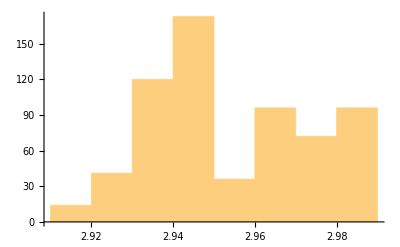

```mathematica
part=All;
Histogram[100Abs[potential[triangles,charges,points⟦part⟧]-values⟦part,1⟧]/values⟦part,1⟧]
```

```mathematica
points=Join@@{Join[Table[{0,0,z},{z,-10,-1,0.05}],Table[{0,0,z},{z,1,10,0.05}]],{{0,0,-1},{0,0,1}},Table[{0,0,z},{z,-1,1,0.05}]};
data={points⟦All,3⟧,Re@potential[triangles,charges,points]}ᵀ;
```

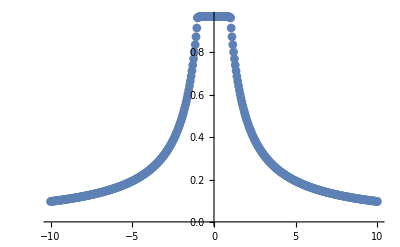

```mathematica
ListPlot[Tooltip@Sort@data,PlotMarkers->Automatic,PlotRange->All]
```

```mathematica
points=Flatten[Table[{x,y,0},{x,-2,2,0.1},{y,-2,2,0.1}],1];
data=Flatten/@({points⟦All,1;;2⟧,Re@potential[triangles,charges,points]}ᵀ);
```

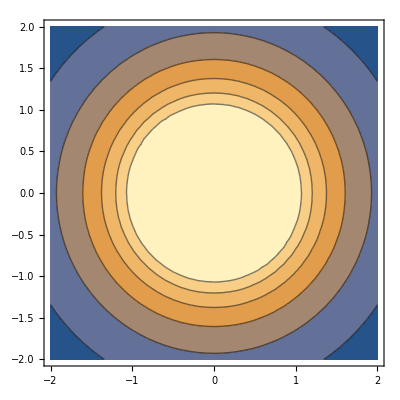

```mathematica
ListContourPlot[data,Contours->Automatic]
```

## 4 Rod

```mathematica
model=ConnectedMeshComponents@Import@"4rod.stl"
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[Show[model,HighlightMesh[model⟦i⟧,Style[1,Red]],ImageSize->30],{i,Length@model}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
voltages={1,0,0,0,0,1};
```

```mathematica
voltages={0,1,0,1,0,0};
```

```mathematica
{nodes,elements}=(NodesElements/@model)ᵀ;
elements+=Prepend[Accumulate@Most[Length/@nodes],0];
nodes=10Join@@nodes;
```

```mathematica
Export["4rod.csv",StringJoin@@Riffle[Join[{ToString@Length@nodes<>","<>ToString@Length@elements,ExportString[nodes,"CSV"]},Flatten[{ToString@Length@#,ExportString[#,"CSV"]}&/@((Reverse/@#)&/@elements),1],{ExportString[{{-0.4,-0.4,21},{0.4,0.4,21},{20,20,1}},"CSV"]}],"\n"],"Text"];
```

```mathematica
elements=Join@@Table[Join[#,{1,voltages⟦i⟧}]&/@elements⟦i⟧,{i,Length@elements}];
triangles=nodes⟦#⟧&/@elements⟦All,1;;3⟧;
```

```mathematica
Export["nodes.csv",nodes];
Export["elements.csv",elements];
```

### BEM

```mathematica
Run["BEM 4rod.csv"];
```

```mathematica
path=FileNameJoin@{NotebookDirectory[],"4rod"};
```

```mathematica
data=Import[path,"Byte"];
pos=Prepend[Flatten@Position[data,10,1,7],0];
{n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum}=Read[StringToStream@FromCharacterCode@data⟦#⟧,Number]&/@(Span@@(#+{1,-1})&/@Partition[pos,2,1]);
data=Partition[ImportString[FromCharacterCode@data⟦Last@pos+1;;-1⟧,"Real64"],n];
```

```mathematica
points=Flatten[Table[{x,y,21},{x,-0.4,0.4,0.01},{y,-0.4,0.4,0.01}],1];
data=Flatten/@({points⟦All,1;;2⟧,Re@potential[triangles,4π (data⟦2⟧+data⟦4⟧),points]}ᵀ);
```

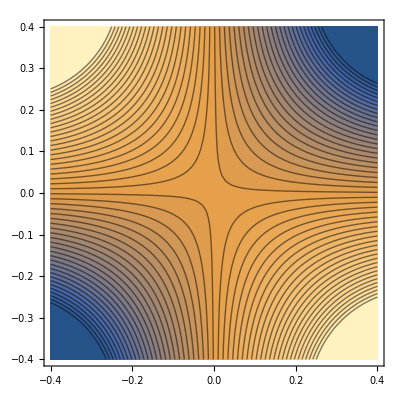

```mathematica
ListContourPlot[data,Contours->50]
```

```mathematica
points=Table[{0,0,z+21},{z,-0.1,0.1,0.001}];
data={points⟦All,3⟧-21,Re@potential[triangles,4π (data⟦1⟧+data⟦6⟧),points]}ᵀ;
```

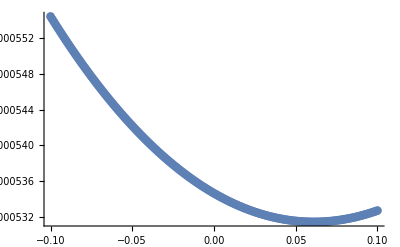

```mathematica
ListLinePlot[data,PlotMarkers->Automatic,PlotRange->Full]
```

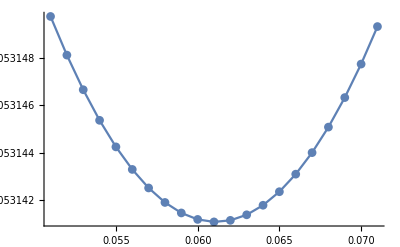

```mathematica
ListLinePlot[data⟦-50;;-30⟧,PlotMarkers->Automatic]
```

```mathematica
Fit[data⟦-50;;-30⟧,{1,x,x^2},x]
```

0.000534576-0.000103558 x+0.000847131 x^2

```mathematica
data=Import[path<>"calc-1","Byte"];
pos=Prepend[Flatten@Position[data,10,1,16],0];
{n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum,xmin,xmax,nx,ymin,ymax,ny,zmin,zmax,nz}=Read[StringToStream@FromCharacterCode@data⟦#⟧,Number]&/@(Span@@(#+{1,-1})&/@Partition[pos,2,1]);
data=Partition[#,nx*ny*nz]&/@Partition[ImportString[FromCharacterCode@data⟦Last@pos+1;;-1⟧,"Real64"],nx*ny*nz*amountOfElectrodes];
```

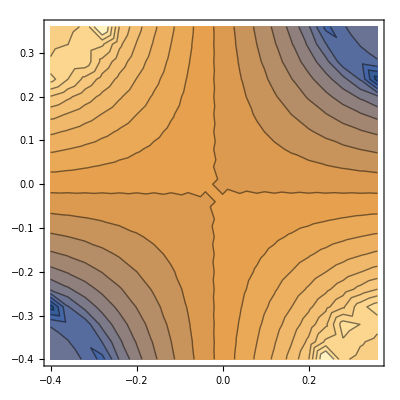

```mathematica
ListContourPlot[Flatten/@({N@Tuples[{xmin+(xmax-xmin)/nx Range[0,nx-1],ymin+(ymax-ymin)/ny Range[0,ny-1]}],data⟦1,2⟧+data⟦1,4⟧}ᵀ),Contours->20]
```

```mathematica
data=Import[path<>"calc-2","Byte"];
pos=Prepend[Flatten@Position[data,10,1,16],0];
{n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum,xmin,xmax,nx,ymin,ymax,ny,zmin,zmax,nz}=Read[StringToStream@FromCharacterCode@data⟦#⟧,Number]&/@(Span@@(#+{1,-1})&/@Partition[pos,2,1]);
data=Partition[#,nx*ny*nz]&/@Partition[ImportString[FromCharacterCode@data⟦Last@pos+1;;-1⟧,"Real64"],nx*ny*nz*amountOfElectrodes];
```

```mathematica
data=N@{zmin+(zmax-zmin)/nz Range[0,nz-1]-21,data⟦1,1⟧+data⟦1,6⟧}ᵀ;
```

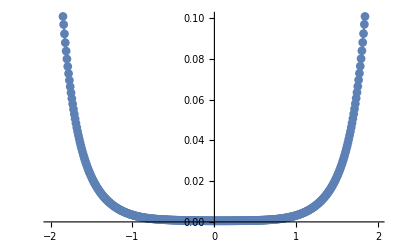

```mathematica
ListLinePlot[data,PlotMarkers->Automatic]
```

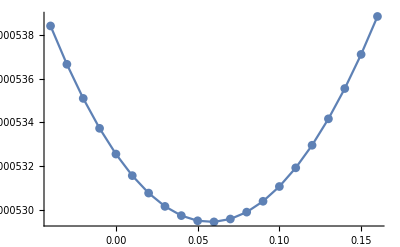

```mathematica
ListLinePlot[data⟦207-10;;207+10⟧,PlotMarkers->Automatic]
```

```mathematica
Fit[data⟦207-10;;207+10⟧,{1,x,x^2},x]
```

0.000532579-0.000107297 x+0.00091746 x^2

### 3D_Potential_CHBIE_FMM

```mathematica
Run["python run.py 4rod"];
Run["3D_Potential_CHBIE_FMM_64"];
```

```mathematica
output=Import["output.dat","Table"];
values=Rest/@output⟦3;;-1⟧;
charges=values⟦All,2⟧;
```

```mathematica
points=Table[{0,0,z+21},{z,-0.1,0.1,0.001}];
data={points⟦All,3⟧-21,Re@potential[triangles,charges,points]}ᵀ;
```

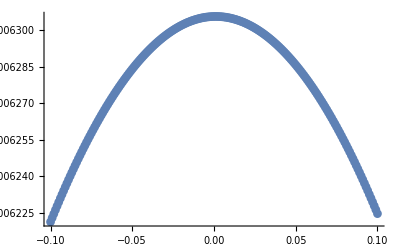

```mathematica
ListLinePlot[data,PlotMarkers->Automatic,PlotRange->Full]
```